### Flight Times

#### Plot for gas flight times (*wrong*)

```mathematica
flightTimeSound={795753,675551,585482,447364,336486};
flightTimeSoundError={ErrorBar@29927,ErrorBar@33533,ErrorBar@36235,ErrorBar@40379,ErrorBar@43705};

flightTimeTerminal={836854,767456,715454,635711,571696};
flightTimeTerminalError={ErrorBar@30776,ErrorBar@33659,ErrorBar@32336,ErrorBar@34729,ErrorBar@36649};

flightTimeMeasured={750000,650000,470000,4,5};
flightTimeMeasuredError={ErrorBar@25000,ErrorBar@25000,ErrorBar@25000,ErrorBar@25000,ErrorBar@25000};

amu={4,20,40,84,131};
```

```mathematica
Needs["ErrorBarPlots`"]
```

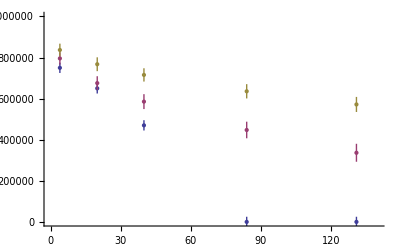

```mathematica
ErrorListPlot[{Transpose[{Transpose[{amu,flightTimeMeasured}],flightTimeMeasuredError}],Transpose[{Transpose[{amu,flightTimeSound}],flightTimeSoundError}],
Transpose[{Transpose[{amu,flightTimeTerminal}],flightTimeTerminalError}]},PlotRange->{{0,140},{0,10^6}}]
```

#### Distance plot Argon

```mathematica
d={9.8,19.7,14.75,17.2,12.25}+2.5;
flightTimesMeasured = {570000,395000,475000,435000,520000};
flightTimesMeasuredError={ErrorBar@10000,ErrorBar@10000,ErrorBar@10000,ErrorBar@10000,ErrorBar@10000};

flightTimesCalculated ={570000,389900,480484,435192,525776};
flightTimeCalculatedlError={ErrorBar@33668,ErrorBar@39103,ErrorBar@36386,ErrorBar@37744,ErrorBar@35027};
```

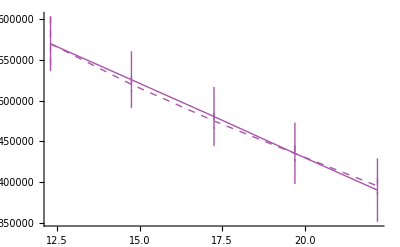

```mathematica
plotArgon=ErrorListPlot[{Sort[Transpose[{Transpose[{d,flightTimesMeasured}],flightTimesMeasuredError}]],Sort[Transpose[{Transpose[{d,flightTimesCalculated}],flightTimeCalculatedlError}]]},Joined->True,PlotStyle->{Directive[Lighter[Purple],Thick,Dashed],Directive[Lighter[Purple],Thick,Dashing[None]]}]
```

#### Distance plot xenon

```mathematica
dXenon={9.8,9.8+2.5,9.8+5,9.8+7.5}+2.5;
flightTimesMeasuredXenon = {390000,310000,220000,140000};
flightTimesMeasuredErrorXenon={ErrorBar@10000,ErrorBar@10000,ErrorBar@10000,ErrorBar@10000};


flightTimesCalculatedXenon ={391371,309406,227441,145476};
flightTimeCalculatedlErrorXenon={ErrorBar@39059,ErrorBar@41518,ErrorBar@43977,ErrorBar@46356};
```

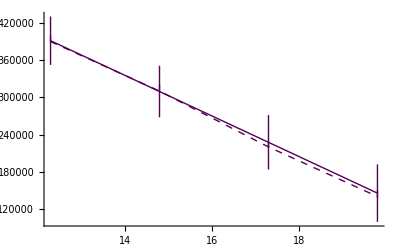

```mathematica
plotXenon=ErrorListPlot[{Sort[Transpose[{Transpose[{dXenon,flightTimesMeasuredXenon}],flightTimesMeasuredErrorXenon}]],Sort[Transpose[{Transpose[{dXenon,flightTimesCalculatedXenon}],flightTimeCalculatedlErrorXenon}]]},Joined->True,PlotStyle->{Directive[Darker@Purple,Thick,Dashed],Directive[Darker@Purple,Thick,Dashing[None]]}]
```

#### plotting

```mathematica
Needs["PlotLegends`"]
```

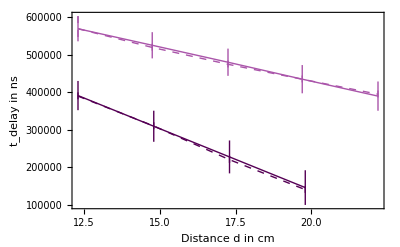

```mathematica
ShowLegend[ErrorListPlot[{
Sort[Transpose[{Transpose[{d,flightTimesMeasured}],flightTimesMeasuredError}]],Sort[Transpose[{Transpose[{d,flightTimesCalculated}],flightTimeCalculatedlError}]],Sort[Transpose[{Transpose[{dXenon,flightTimesMeasuredXenon}],flightTimesMeasuredErrorXenon}]],Sort[Transpose[{Transpose[{dXenon,flightTimesCalculatedXenon}],flightTimeCalculatedlErrorXenon}]]},Joined->True,PlotStyle->{Directive[Lighter[Purple],Thick,Dashed],Directive[Lighter[Purple],Thick,Dashing[None]],Directive[Darker@Purple,Thick,Dashed],Directive[Darker@Purple,Thick,Dashing[None]]},Frame->True,Axes->False,FrameLabel->{"Distance d in cm","t_delay in ns"},FrameStyle->Directive[12]],{{{Graphics[{Lighter[Purple],Dashed,Thick,Line[{{0,0},{2,0}}]}],"Argon measured"},{Graphics[{Lighter[Purple],Dashing[None],Thick,Line[{{0,0},{2,0}}]}],"Argon calculated"},{Graphics[{Darker@Purple,Dashed,Thick,Line[{{0,0},{2,0}}]}],"Xenon measured"},{Graphics[{Darker@Purple,Dashing[None],Thick,Line[{{0,0},{2,0}}]}],"Xenon calculated"}},LegendPosition->{-0.6,-0.4},LegendShadow->None,LegendTextSpace->4,LegendBorder->None,LegendSpacing->0,LegendBorderSpace->0,LegendLabelSpace->0,LegendBackground->White,LegendSize->0.5}]
```